```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tomikbaikie/MIT Dropbox/Tomi Baikie/Tomi/Projects/LSC_Singlet_Fission/Data_Figures/EQE_modelling

```mathematica
(*Constants*)
c = 299792458.;(*units:m/s*)
h = 6.6260695729*10^(-34) // N; (*units:J s-Planck's Constant*)
h2 = 4.136*10^(-15) // N; (*units:eV s-Planck's Constant*)
q = 1.60217657*10^(-19) // N; (*units:Coulombs*)
k = 8.617*10^(−5) // N;(*units:eV/K*)
T = 298.15 // N;(*units:K*)
fac = h *c *10^(9)/q // N ;
k2 = 1.3807*10^(-23) // N;  (*J/K*)
ClearSystemCache[];

(*Temperature dependent intrinsic charge carrier concentration from \
K.Misiakos,et al.Accurate Measurements of the Silicon Intrinsic \
Carrier Density from 78 to 340 K.J.Appl.Phys.1993,74,3293–3297 \
DOI:10.1063/1.354551*)
(*units:m^-3*)
Sini[T_Real] := 5.29*10^(19)*(T/300.)^(2.54)*Exp[-6726./T]*10^(6);

(*Temperature dependent bandgap is calculated using Varshni\
’s empirical equation with values from the book \
Physics of Semiconductor Devices Physics of Semiconductor \
Devices,Wiley-Interscience,1995 from Sze*)

ClearAll[SiBandgap]
SiBandgap[Temp_Real] := 1.17 - 4.73*10^(-4)* Temp^(2)/(Temp + 636.);

(*Temperature dependent Auger coefficient from J.Dziewior et al.Auger \
Coefficients for Highly Doped and Highly Excited \
Silicon.Appl.Phys.Lett.1977,346,11–14 DOI:10.1063/1.89694*)
(*Cn=2.8 x 10^-31 cm^6/s Cp=0.99 x 10^-31cm^6/s units:m^6/s*)
SiC[T_Real] := (2.8 + 0.99)*10^(-43)*(T/300.)^(1./2.);
(* Current  Densities   *) 
(*Current densities*)
(*Radiative recombination current density*)
JRad0Si = 
  q*2*Pi/(c^(2)*h2^(3))*
   NIntegrate[En^(2)/(Exp[En/(k*T)] - 1), {En, SiBandgap[T], 4.4}];
JRSi[V_Real, Il_Real, Rs_Real] := 
  JRad0Si*(Exp[(V + Il*Rs*0.0001)/(k T)] - 1);

(*Auger recombination current density*)
JRAuger[V_Real, Il_Real, Rs_Real, L_Real] := 
  q*L*SiC[T]*Sini[T]^3 (Exp[(3 (V + Il*Rs*0.0001))/(2*k*T)] - 1);

(*Non-radiative recombination current density*)
JRnon[V_Real, Il_Real, Rs_Real, INR_Real] := 
  INR*10^-42 Sini[T]^2 (Exp[(V + Il*Rs*0.0001)/(k T)] - 1);



(*Resistance*)
Resistance[V_Real, Il_Real, Rs_Real, 
   Rsh_Real] := (V + Il*Rs*0.0001)/(Rsh*0.0001);
(* More Constants   *) 
(*Fitting values*)
(*Thickness of silicon for Auger recombination in m*)
thicknesses = {(*1*)1.7*10^-4,(*2*)1.8*10^-4,(*assumption*)(*3*)
   1.8*10^-4,(*4*)1.9*10^-4,(*5*)1.8*10^-4,(*assumption*)(*6*)
   1.8*10^-4,(*assumption*)(*7*)1.9*10^-4,(*8*)1.95*10^-4,(*9*)
   1.5*10^-4,(*10*)2*10^-4,(*11*)1.5*10^-4,(*12*)2*10^-4,(*13*)
   2*10^-4};

(*Parasitic resistances in ohm cm^2*)
Rs = {(*1*)1.48,(*2*)1.15,(*3*)1.35,(*4*)0.82,(*5*)1.28,(*6*)0.73,(*7*)
   0.59,(*8*)0.6,(*9*)0.67,(*10*)0.75,(*11*)0.47,(*12*)0.31,(*13*)
   0.08};
Rsh = {(*1*)1800,(*2*)1300,(*3*)1800,(*4*)1800,(*5*)1200,(*6*)
   2000,(*7*)2000,(*8*)3000,(*9*)2000,(*10*)800,(*11*)4000,(*12*)
   6000,(*13*)10000};

(*Non-radiative recombination*)
INR = {(*1*)58,(*2*)85.7,(*3*)56,(*4*)58,(*5*)10.5,(*6*)43,(*7*)
   35,(*8*)24.1,(*9*)1.5,(*10*)1.95,(*11*)1.7,(*12*)1.41,(*13*)
   1.88485};

(* IV Characteristics   *) 
(*Import JV characteristic*)
IV13 = Import["./Record_Si_cell/13_IV.csv"];
(*Import EQE*)
EQE13 = Import["./Record_Si_cell/13_EQE.csv"];
intEQE13 = Interpolation[EQE13, InterpolationOrder -> 0];
```

```mathematica
photonsin=x; 
photonsout =
```

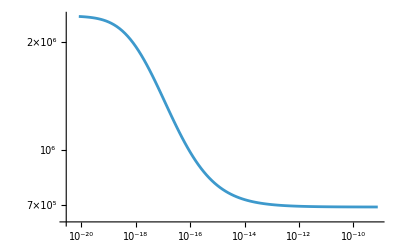

```mathematica
plvsktta=ToExpression[Import["PL_tta_relationship.csv","CSV"]];
plvsktta2 = plvsktta;
plvsktta2[[;;,2]]=Abs[plvsktta2[[;;,2]]];
ListLogLogPlot[plvsktta2,Joined->True]
plvsktta2int = Interpolation[plvsktta2];
0.3*plvsktta2int[10^-19]/2.2736628330122125*^6
```

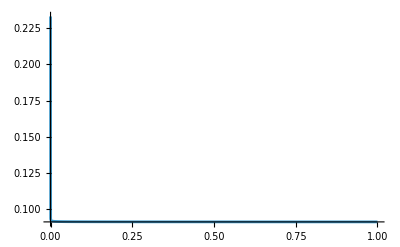

```mathematica
Plot[0.3*plvsktta2int[x]/2.2736628330122125*^6,{x,10^-19,10^-10},PlotRange->All]
```

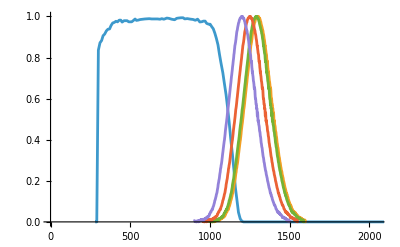

```mathematica
dotpl=Import["dot_pl.csv","CSV"];

shift[x_]:=Module[{output}, 
output = dotpl;
output[[;;,1]]=output[[;;,1]]-x;
Return[output];
]

ListPlot[{EQE13nm,dotpl,shift[10],shift[50],shift[100]},Joined->True]
```

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)]
kttatotry = logspace[-21,-15,30]
```

{1.×10^-22,1.48735×10^-22,2.21222×10^-22,3.29034×10^-22,4.8939×10^-22,7.27895×10^-22,1.08264×10^-21,1.61026×10^-21,2.39503×10^-21,3.56225×10^-21,5.29832×10^-21,7.88046×10^-21,1.1721×10^-20,1.74333×10^-20,2.59294×10^-20,3.85662×10^-20,5.73615×10^-20,8.53168×10^-20,1.26896×10^-19,1.88739×10^-19,2.80722×10^-19,4.17532×10^-19,6.21017×10^-19,9.23671×10^-19,1.37382×10^-18,2.04336×10^-18,3.0392×10^-18,4.52035×10^-18,6.72336×10^-18,1.×10^-17}

```mathematica
tolambda[energyinEv_]:=Module[{},
Return[h*c/(energyinEv*q)]
]
```

```mathematica
eqeint = Interpolation[EQE13nm,InterpolationOrder->0];
plint0 = Interpolation[shift[0],InterpolationOrder->0];
allpl = NIntegrate[plint0[x],{x,1000,1500}];
shifts = Table[
plint = Interpolation[Prepend[shift[i],{280,0}],InterpolationOrder->0];
(*Plot[eqeint[x]*plint[x],{x,500,1500},PlotRange->All];*);
ploverlap = NIntegrate[eqeint[x]*plint[x],{x,500,1500}];
percent = ploverlap/allpl;
jg =1000;
maxeff =0.3*plvsktta2int[x]/2.2736628330122125*^6; 
{i,x, lossesplease[jg*maxeff*percent][[2]]},{i,1,300,10},{x,kttatotry}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

{{{1,1.×10^-22,4.06733},{1,1.48735×10^-22,4.06722},{1,2.21222×10^-22,4.06706},{1,3.29034×10^-22,4.06682},{1,4.8939×10^-22,4.06647},{1,7.27895×10^-22,4.06594},{1,1.08264×10^-21,4.06516},{1,1.61026×10^-21,4.06399},{1,2.39503×10^-21,4.06227},{1,3.56225×10^-21,4.05973},{1,5.29832×10^-21,4.05597},{1,7.88046×10^-21,4.05046},{1,1.1721×10^-20,4.0424},{1,1.74333×10^-20,4.03073},{1,2.59294×10^-20,4.014},{1,3.85662×10^-20,3.99035},{1,5.73615×10^-20,3.95753},{1,8.53168×10^-20,3.91296},{1,1.26896×10^-19,3.85276},{1,1.88739×10^-19,3.77756},{1,2.80722×10^-19,3.68375},{1,4.17532×10^-19,3.56902},{1,6.21017×10^-19,3.43511},{1,9.23671×10^-19,3.28712},{1,1.37382×10^-18,3.12102},{1,2.04336×10^-18,2.94594},{1,3.0392×10^-18,2.764},{1,4.52035×10^-18,2.57996},{1,6.72336×10^-18,2.39951},{1,1.×10^-17,2.22594}},{{11,1.×10^-22,4.97591},{11,1.48735×10^-22,4.97578},{11,2.21222×10^-22,4.97559},{11,3.29034×10^-22,4.9753},{11,4.8939×10^-22,4.97487},{11,7.27895×10^-22,4.97423},{11,1.08264×10^-21,4.97328},{11,1.61026×10^-21,4.97188},{11,2.39503×10^-21,4.96979},{11,3.56225×10^-21,4.96671},{11,5.29832×10^-21,4.96217},{11,7.88046×10^-21,4.9555},{11,1.1721×10^-20,4.94576},{11,1.74333×10^-20,4.93164},{11,2.59294×10^-20,4.9114},{11,3.85662×10^-20,4.8828},{11,5.73615×10^-20,4.84037},{11,8.53168×10^-20,4.78694},{11,1.26896×10^-19,4.71623},{11,1.88739×10^-19,4.62605},{11,2.80722×10^-19,4.51177},{11,4.17532×10^-19,4.37462},{11,6.21017×10^-19,4.21409},{11,9.23671×10^-19,4.03198},{11,1.37382×10^-18,3.83073},{11,2.04336×10^-18,3.61801},{11,3.0392×10^-18,3.39882},{11,4.52035×10^-18,3.17508},{11,6.72336×10^-18,2.95741},{11,1.×10^-17,2.7474}},{{21,1.×10^-22,6.13298},{21,1.48735×10^-22,6.13282},{21,2.21222×10^-22,6.13258},{21,3.29034×10^-22,6.13223},{21,4.8939×10^-22,6.1317},{21,7.27895×10^-22,6.13093},{21,1.08264×10^-21,6.12977},{21,1.61026×10^-21,6.12805},{21,2.39503×10^-21,6.12551},{21,3.56225×10^-21,6.12176},{21,5.29832×10^-21,6.11621},{21,7.88046×10^-21,6.10808},{21,1.1721×10^-20,6.09619},{21,1.74333×10^-20,6.07896},{21,2.59294×10^-20,6.05427},{21,3.85662×10^-20,6.01938},{21,5.73615×10^-20,5.97094},{21,8.53168×10^-20,5.90517},{21,1.26896×10^-19,5.81812},{21,1.88739×10^-19,5.70474},{21,2.80722×10^-19,5.56626},{21,4.17532×10^-19,5.39892},{21,6.21017×10^-19,5.20305},{21,9.23671×10^-19,4.98084},{21,1.37382×10^-18,4.73475},{21,2.04336×10^-18,4.47628},{21,3.0392×10^-18,4.2077},{21,4.52035×10^-18,3.936},{21,6.72336×10^-18,3.66841},{21,1.×10^-17,3.41212}},{{31,1.×10^-22,7.58077},{31,1.48735×10^-22,7.58057},{31,2.21222×10^-22,7.58028},{31,3.29034×10^-22,7.57985},{31,4.8939×10^-22,7.57921},{31,7.27895×10^-22,7.57825},{31,1.08264×10^-21,7.57684},{31,1.61026×10^-21,7.57474},{31,2.39503×10^-21,7.57162},{31,3.56225×10^-21,7.56702},{31,5.29832×10^-21,7.56023},{31,7.88046×10^-21,7.55026},{31,1.1721×10^-20,7.53569},{31,1.74333×10^-20,7.51458},{31,2.59294×10^-20,7.48433},{31,3.85662×10^-20,7.44157},{31,5.73615×10^-20,7.38222},{31,8.53168×10^-20,7.30163},{31,1.26896×10^-19,7.19497},{31,1.88739×10^-19,7.05776},{31,2.80722×10^-19,6.8858},{31,4.17532×10^-19,6.67971},{31,6.21017×10^-19,6.44072},{31,9.23671×10^-19,6.16843},{31,1.37382×10^-18,5.86905},{31,2.04336×10^-18,5.54946},{31,3.0392×10^-18,5.22031},{31,4.52035×10^-18,4.88734},{31,6.72336×10^-18,4.55865},{31,1.×10^-17,4.24455}},{{41,1.×10^-22,9.36146},{41,1.48735×10^-22,9.36122},{41,2.21222×10^-22,9.36086},{41,3.29034×10^-22,9.36033},{41,4.8939×10^-22,9.35954},{41,7.27895×10^-22,9.35838},{41,1.08264×10^-21,9.35664},{41,1.61026×10^-21,9.35406},{41,2.39503×10^-21,9.35025},{41,3.56225×10^-21,9.3446},{41,5.29832×10^-21,9.33628},{41,7.88046×10^-21,9.32405},{41,1.1721×10^-20,9.30619},{41,1.74333×10^-20,9.28032},{41,2.59294×10^-20,9.24323},{41,3.85662×10^-20,9.19081},{41,5.73615×10^-20,9.11805},{41,8.53168×10^-20,9.01925},{41,1.26896×10^-19,8.88849},{41,1.88739×10^-19,8.72027},{41,2.80722×10^-19,8.5104},{41,4.17532×10^-19,8.25755},{41,6.21017×10^-19,7.96327},{41,9.23671×10^-19,7.62942},{41,1.37382×10^-18,7.26236},{41,2.04336×10^-18,6.86991},{41,3.0392×10^-18,6.46632},{41,4.52035×10^-18,6.05804},{41,6.72336×10^-18,5.6543},{41,1.×10^-17,5.26913}},{{51,1.×10^-22,11.5162},{51,1.48735×10^-22,11.5159},{51,2.21222×10^-22,11.5155},{51,3.29034×10^-22,11.5148},{51,4.8939×10^-22,11.5139},{51,7.27895×10^-22,11.5124},{51,1.08264×10^-21,11.5103},{51,1.61026×10^-21,11.5072},{51,2.39503×10^-21,11.5025},{51,3.56225×10^-21,11.4956},{51,5.29832×10^-21,11.4854},{51,7.88046×10^-21,11.4705},{51,1.1721×10^-20,11.4486},{51,1.74333×10^-20,11.4071},{51,2.59294×10^-20,11.3621},{51,3.85662×10^-20,11.2985},{51,5.73615×10^-20,11.2103},{51,8.53168×10^-20,11.0905},{51,1.26896×10^-19,10.9319},{51,1.88739×10^-19,10.728},{51,2.80722×10^-19,10.4752},{51,4.17532×10^-19,10.166},{51,6.21017×10^-19,9.80211},{51,9.23671×10^-19,9.39769},{51,1.37382×10^-18,8.94872},{51,2.04336×10^-18,8.46949},{51,3.0392×10^-18,7.97471},{51,4.52035×10^-18,7.47529},{51,6.72336×10^-18,6.98259},{51,1.×10^-17,6.50977}},{{61,1.×10^-22,14.085},{61,1.48735×10^-22,14.0847},{61,2.21222×10^-22,14.0841},{61,3.29034×10^-22,14.0834},{61,4.8939×10^-22,14.0822},{61,7.27895×10^-22,14.0804},{61,1.08264×10^-21,14.0779},{61,1.61026×10^-21,14.074},{61,2.39503×10^-21,14.0683},{61,3.56225×10^-21,14.0599},{61,5.29832×10^-21,14.0475},{61,7.88046×10^-21,14.0293},{61,1.1721×10^-20,14.0027},{61,1.74333×10^-20,13.9642},{61,2.59294×10^-20,13.909},{61,3.85662×10^-20,13.8309},{61,5.73615×10^-20,13.7226},{61,8.53168×10^-20,13.5674},{61,1.26896×10^-19,13.3807},{61,1.88739×10^-19,13.1291},{61,2.80722×10^-19,12.8177},{61,4.17532×10^-19,12.4417},{61,6.21017×10^-19,12.0034},{61,9.23671×10^-19,11.5062},{61,1.37382×10^-18,10.9535},{61,2.04336×10^-18,10.3749},{61,3.0392×10^-18,9.76951},{61,4.52035×10^-18,9.16553},{61,6.72336×10^-18,8.56553},{61,1.×10^-17,7.98976}},{{71,1.×10^-22,17.1052},{71,1.48735×10^-22,17.1047},{71,2.21222×10^-22,17.1041},{71,3.29034×10^-22,17.1031},{71,4.8939×10^-22,17.1017},{71,7.27895×10^-22,17.0996},{71,1.08264×10^-21,17.0965},{71,1.61026×10^-21,17.0918},{71,2.39503×10^-21,17.0849},{71,3.56225×10^-21,17.0748},{71,5.29832×10^-21,17.0598},{71,7.88046×10^-21,17.0377},{71,1.1721×10^-20,17.0055},{71,1.74333×10^-20,16.9589},{71,2.59294×10^-20,16.8921},{71,3.85662×10^-20,16.7976},{71,5.73615×10^-20,16.6664},{71,8.53168×10^-20,16.4884},{71,1.26896×10^-19,16.2527},{71,1.88739×10^-19,15.9495},{71,2.80722×10^-19,15.5712},{71,4.17532×10^-19,15.1141},{71,6.21017×10^-19,14.5791},{71,9.23671×10^-19,13.9855},{71,1.37382×10^-18,13.3237},{71,2.04336×10^-18,12.6174},{71,3.0392×10^-18,11.8897},{71,4.52035×10^-18,11.1457},{71,6.72336×10^-18,10.4269},{71,1.×10^-17,9.72631}},{{81,1.×10^-22,20.6098},{81,1.48735×10^-22,20.6093},{81,2.21222×10^-22,20.6085},{81,3.29034×10^-22,20.6073},{81,4.8939×10^-22,20.6056},{81,7.27895×10^-22,20.6031},{81,1.08264×10^-21,20.5993},{81,1.61026×10^-21,20.5938},{81,2.39503×10^-21,20.5855},{81,3.56225×10^-21,20.5733},{81,5.29832×10^-21,20.5552},{81,7.88046×10^-21,20.5287},{81,1.1721×10^-20,20.49},{81,1.74333×10^-20,20.434},{81,2.59294×10^-20,20.3536},{81,3.85662×10^-20,20.24},{81,5.73615×10^-20,20.0824},{81,8.53168×10^-20,19.8683},{81,1.26896×10^-19,19.585},{81,1.88739×10^-19,19.2204},{81,2.80722×10^-19,18.7695},{81,4.17532×10^-19,18.2245},{81,6.21017×10^-19,17.5867},{81,9.23671×10^-19,16.8631},{81,1.37382×10^-18,16.0675},{81,2.04336×10^-18,15.2183},{81,3.0392×10^-18,14.3462},{81,4.52035×10^-18,13.461},{81,6.72336×10^-18,12.5877},{81,1.×10^-17,11.7526}},{{91,1.×10^-22,24.6159},{91,1.48735×10^-22,24.6153},{91,2.21222×10^-22,24.6144},{91,3.29034×10^-22,24.613},{91,4.8939×10^-22,24.611},{91,7.27895×10^-22,24.608},{91,1.08264×10^-21,24.6036},{91,1.61026×10^-21,24.597},{91,2.39503×10^-21,24.5872},{91,3.56225×10^-21,24.5727},{91,5.29832×10^-21,24.5583},{91,7.88046×10^-21,24.5267},{91,1.1721×10^-20,24.4742},{91,1.74333×10^-20,24.4079},{91,2.59294×10^-20,24.3128},{91,3.85662×10^-20,24.1784},{91,5.73615×10^-20,23.9919},{91,8.53168×10^-20,23.7386},{91,1.26896×10^-19,23.4033},{91,1.88739×10^-19,22.972},{91,2.80722×10^-19,22.434},{91,4.17532×10^-19,21.7837},{91,6.21017×10^-19,21.0227},{91,9.23671×10^-19,20.1593},{91,1.37382×10^-18,19.2099},{91,2.04336×10^-18,18.205},{91,3.0392×10^-18,17.1608},{91,4.52035×10^-18,16.1045},{91,6.72336×10^-18,15.0623},{91,1.×10^-17,14.0695}},{{101,1.×10^-22,29.1637},{101,1.48735×10^-22,29.163},{101,2.21222×10^-22,29.1619},{101,3.29034×10^-22,29.1603},{101,4.8939×10^-22,29.1579},{101,7.27895×10^-22,29.1544},{101,1.08264×10^-21,29.1491},{101,1.61026×10^-21,29.1413},{101,2.39503×10^-21,29.1297},{101,3.56225×10^-21,29.1126},{101,5.29832×10^-21,29.0873},{101,7.88046×10^-21,29.0502},{101,1.1721×10^-20,28.996},{101,1.74333×10^-20,28.9175},{101,2.59294×10^-20,28.8049},{101,3.85662×10^-20,28.6458},{101,5.73615×10^-20,28.4249},{101,8.53168×10^-20,28.1251},{101,1.26896×10^-19,27.7192},{101,1.88739×10^-19,27.2046},{101,2.80722×10^-19,26.5806},{101,4.17532×10^-19,25.8108},{101,6.21017×10^-19,24.9},{101,9.23671×10^-19,23.8863},{101,1.37382×10^-18,22.7717},{101,2.04336×10^-18,21.5819},{101,3.0392×10^-18,20.3456},{101,4.52035×10^-18,19.0958},{101,6.72336×10^-18,17.8722},{101,1.×10^-17,16.6917}},{{111,1.×10^-22,34.2437},{111,1.48735×10^-22,34.2428},{111,2.21222×10^-22,34.2416},{111,3.29034×10^-22,34.2397},{111,4.8939×10^-22,34.2369},{111,7.27895×10^-22,34.2327},{111,1.08264×10^-21,34.2265},{111,1.61026×10^-21,34.2173},{111,2.39503×10^-21,34.2037},{111,3.56225×10^-21,34.1836},{111,5.29832×10^-21,34.1539},{111,7.88046×10^-21,34.1104},{111,1.1721×10^-20,34.0467},{111,1.74333×10^-20,33.9545},{111,2.59294×10^-20,33.8223},{111,3.85662×10^-20,33.6355},{111,5.73615×10^-20,33.3762},{111,8.53168×10^-20,33.0241},{111,1.26896×10^-19,32.5581},{111,1.88739×10^-19,31.9586},{111,2.80722×10^-19,31.2106},{111,4.17532×10^-19,30.3068},{111,6.21017×10^-19,29.2495},{111,9.23671×10^-19,28.0591},{111,1.37382×10^-18,26.7502},{111,2.04336×10^-18,25.3397},{111,3.0392×10^-18,23.8998},{111,4.52035×10^-18,22.4433},{111,6.72336×10^-18,21.0063},{111,1.×10^-17,19.6199}},{{121,1.×10^-22,39.8432},{121,1.48735×10^-22,39.8422},{121,2.21222×10^-22,39.8407},{121,3.29034×10^-22,39.8385},{121,4.8939×10^-22,39.8353},{121,7.27895×10^-22,39.8304},{121,1.08264×10^-21,39.8232},{121,1.61026×10^-21,39.8125},{121,2.39503×10^-21,39.7967},{121,3.56225×10^-21,39.7733},{121,5.29832×10^-21,39.7387},{121,7.88046×10^-21,39.688},{121,1.1721×10^-20,39.6139},{121,1.74333×10^-20,39.5065},{121,2.59294×10^-20,39.3526},{121,3.85662×10^-20,39.1351},{121,5.73615×10^-20,38.8332},{121,8.53168×10^-20,38.4232},{121,1.26896×10^-19,37.8806},{121,1.88739×10^-19,37.1754},{121,2.80722×10^-19,36.3116},{121,4.17532×10^-19,35.2677},{121,6.21017×10^-19,34.0458},{121,9.23671×10^-19,32.6597},{121,1.37382×10^-18,31.1356},{121,2.04336×10^-18,29.5087},{121,3.0392×10^-18,27.8182},{121,4.52035×10^-18,26.1342},{121,6.72336×10^-18,24.4547},{121,1.×10^-17,22.8535}},{{131,1.×10^-22,45.9325},{131,1.48735×10^-22,45.9313},{131,2.21222×10^-22,45.9296},{131,3.29034×10^-22,45.9271},{131,4.8939×10^-22,45.9233},{131,7.27895×10^-22,45.9177},{131,1.08264×10^-21,45.9094},{131,1.61026×10^-21,45.897},{131,2.39503×10^-21,45.8788},{131,3.56225×10^-21,45.8517},{131,5.29832×10^-21,45.8118},{131,7.88046×10^-21,45.7533},{131,1.1721×10^-20,45.6677},{131,1.74333×10^-20,45.5438},{131,2.59294×10^-20,45.3661},{131,3.85662×10^-20,45.1139},{131,5.73615×10^-20,44.7681},{131,8.53168×10^-20,44.2985},{131,1.26896×10^-19,43.6771},{131,1.88739×10^-19,42.8776},{131,2.80722×10^-19,41.8803},{131,4.17532×10^-19,40.675},{131,6.21017×10^-19,39.2642},{131,9.23671×10^-19,37.6638},{131,1.37382×10^-18,35.9073},{131,2.04336×10^-18,34.0441},{131,3.0392×10^-18,32.1079},{131,4.52035×10^-18,30.1493},{131,6.72336×10^-18,28.226},{131,1.×10^-17,26.3769}},{{141,1.×10^-22,52.4287},{141,1.48735×10^-22,52.4274},{141,2.21222×10^-22,52.4255},{141,3.29034×10^-22,52.4226},{141,4.8939×10^-22,52.4184},{141,7.27895×10^-22,52.412},{141,1.08264×10^-21,52.4027},{141,1.61026×10^-21,52.4211},{141,2.39503×10^-21,52.4},{141,3.56225×10^-21,52.3377},{141,5.29832×10^-21,52.2928},{141,7.88046×10^-21,52.2268},{141,1.1721×10^-20,52.1304},{141,1.74333×10^-20,51.9908},{141,2.59294×10^-20,51.8246},{141,3.85662×10^-20,51.5077},{141,5.73615×10^-20,51.115},{141,8.53168×10^-20,50.6266},{141,1.26896×10^-19,49.9153},{141,1.88739×10^-19,48.9681},{141,2.80722×10^-19,47.8354},{141,4.17532×10^-19,46.4786},{141,6.21017×10^-19,44.8644},{141,9.23671×10^-19,43.0469},{141,1.37382×10^-18,41.0485},{141,2.04336×10^-18,38.9153},{141,3.0392×10^-18,36.6954},{141,4.52035×10^-18,34.471},{141,6.72336×10^-18,32.2766},{141,1.×10^-17,30.1594}},{{151,1.×10^-22,59.444},{151,1.48735×10^-22,59.4425},{151,2.21222×10^-22,59.4403},{151,3.29034×10^-22,59.437},{151,4.8939×10^-22,59.4322},{151,7.27895×10^-22,59.425},{151,1.08264×10^-21,59.4142},{151,1.61026×10^-21,59.3983},{151,2.39503×10^-21,59.3748},{151,3.56225×10^-21,59.3399},{151,5.29832×10^-21,59.2885},{151,7.88046×10^-21,59.213},{151,1.1721×10^-20,59.1027},{151,1.74333×10^-20,58.9429},{151,2.59294×10^-20,58.7139},{151,3.85662×10^-20,58.3902},{151,5.73615×10^-20,57.9408},{151,8.53168×10^-20,57.3307},{151,1.26896×10^-19,56.5225},{151,1.88739×10^-19,55.4843},{151,2.80722×10^-19,54.2009},{151,4.17532×10^-19,52.6215},{151,6.21017×10^-19,50.8282},{151,9.23671×10^-19,48.7347},{151,1.37382×10^-18,46.4961},{151,2.04336×10^-18,44.0816},{151,3.0392×10^-18,41.5851},{151,4.52035×10^-18,39.0597},{151,6.72336×10^-18,36.566},{151,1.×10^-17,34.1816}},{{161,1.×10^-22,66.7348},{161,1.48735×10^-22,66.7331},{161,2.21222×10^-22,66.7306},{161,3.29034×10^-22,66.727},{161,4.8939×10^-22,66.7216},{161,7.27895×10^-22,66.7135},{161,1.08264×10^-21,66.7015},{161,1.61026×10^-21,66.6837},{161,2.39503×10^-21,66.6574},{161,3.56225×10^-21,66.6185},{161,5.29832×10^-21,66.561},{161,7.88046×10^-21,66.4767},{161,1.1721×10^-20,66.3535},{161,1.74333×10^-20,66.175},{161,2.59294×10^-20,65.9192},{161,3.85662×10^-20,65.5576},{161,5.73615×10^-20,65.0557},{161,8.53168×10^-20,64.3741},{161,1.26896×10^-19,63.4721},{161,1.88739×10^-19,62.3117},{161,2.80722×10^-19,60.8639},{161,4.17532×10^-19,59.1145},{161,6.21017×10^-19,57.0667},{161,9.23671×10^-19,54.7437},{161,1.37382×10^-18,52.1886},{161,2.04336×10^-18,49.5127},{161,3.0392×10^-18,46.7017},{161,4.52035×10^-18,43.8669},{161,6.72336×10^-18,41.0838},{161,1.×10^-17,38.3987}},{{171,1.×10^-22,74.2975},{171,1.48735×10^-22,74.2957},{171,2.21222×10^-22,74.2929},{171,3.29034×10^-22,74.2888},{171,4.8939×10^-22,74.2828},{171,7.27895×10^-22,74.2738},{171,1.08264×10^-21,74.2604},{171,1.61026×10^-21,74.2405},{171,2.39503×10^-21,74.2111},{171,3.56225×10^-21,74.1676},{171,5.29832×10^-21,74.1035},{171,7.88046×10^-21,74.0093},{171,1.1721×10^-20,73.8718},{171,1.74333×10^-20,73.6724},{171,2.59294×10^-20,73.3867},{171,3.85662×10^-20,72.9829},{171,5.73615×10^-20,72.4224},{171,8.53168×10^-20,71.6612},{171,1.26896×10^-19,70.6539},{171,1.88739×10^-19,69.358},{171,2.80722×10^-19,67.7535},{171,4.17532×10^-19,65.8149},{171,6.21017×10^-19,63.5457},{171,9.23671×10^-19,60.9715},{171,1.37382×10^-18,58.141},{171,2.04336×10^-18,55.1198},{171,3.0392×10^-18,51.9794},{171,4.52035×10^-18,48.8282},{171,6.72336×10^-18,45.7503},{171,1.×10^-17,42.7687}},{{181,1.×10^-22,82.036},{181,1.48735×10^-22,82.034},{181,2.21222×10^-22,82.031},{181,3.29034×10^-22,82.0265},{181,4.8939×10^-22,82.0198},{181,7.27895×10^-22,82.0099},{181,1.08264×10^-21,81.9952},{181,1.61026×10^-21,81.9734},{181,2.39503×10^-21,81.941},{181,3.56225×10^-21,81.8932},{181,5.29832×10^-21,81.8227},{181,7.88046×10^-21,81.7192},{181,1.1721×10^-20,81.5679},{181,1.74333×10^-20,81.3487},{181,2.59294×10^-20,81.0345},{181,3.85662×10^-20,80.5905},{181,5.73615×10^-20,79.9742},{181,8.53168×10^-20,79.1373},{181,1.26896×10^-19,78.0296},{181,1.88739×10^-19,76.6046},{181,2.80722×10^-19,74.8269},{181,4.17532×10^-19,72.6786},{181,6.21017×10^-19,70.1641},{181,9.23671×10^-19,67.327},{181,1.37382×10^-18,64.2148},{181,2.04336×10^-18,60.8927},{181,3.0392×10^-18,57.4405},{181,4.52035×10^-18,53.9627},{181,6.72336×10^-18,50.5444},{181,1.×10^-17,47.2284}},{{191,1.×10^-22,89.8794},{191,1.48735×10^-22,89.8771},{191,2.21222×10^-22,89.8738},{191,3.29034×10^-22,89.8689},{191,4.8939×10^-22,89.8615},{191,7.27895×10^-22,89.8506},{191,1.08264×10^-21,89.8344},{191,1.61026×10^-21,89.8104},{191,2.39503×10^-21,89.7749},{191,3.56225×10^-21,89.7223},{191,5.29832×10^-21,89.6448},{191,7.88046×10^-21,89.5308},{191,1.1721×10^-20,89.3645},{191,1.74333×10^-20,89.1234},{191,2.59294×10^-20,88.7591},{191,3.85662×10^-20,88.2895},{191,5.73615×10^-20,87.6117},{191,8.53168×10^-20,86.6912},{191,1.26896×10^-19,85.4793},{191,1.88739×10^-19,83.9058},{191,2.80722×10^-19,81.9837},{191,4.17532×10^-19,79.6389},{191,6.21017×10^-19,76.8943},{191,9.23671×10^-19,73.7807},{191,1.37382×10^-18,70.3573},{191,2.04336×10^-18,66.7235},{191,3.0392×10^-18,62.9555},{191,4.52035×10^-18,59.1438},{191,6.72336×10^-18,55.3833},{191,1.×10^-17,51.7328}},{{201,1.×10^-22,97.7432},{201,1.48735×10^-22,97.7407},{201,2.21222×10^-22,97.7371},{201,3.29034×10^-22,97.7318},{201,4.8939×10^-22,97.7238},{201,7.27895×10^-22,97.712},{201,1.08264×10^-21,97.6945},{201,1.61026×10^-21,97.6685},{201,2.39503×10^-21,97.63},{201,3.56225×10^-21,97.573},{201,5.29832×10^-21,97.4889},{201,7.88046×10^-21,97.3655},{201,1.1721×10^-20,97.1852},{201,1.74333×10^-20,96.924},{201,2.59294×10^-20,96.5495},{201,3.85662×10^-20,96.0203},{201,5.73615×10^-20,95.2857},{201,8.53168×10^-20,94.2276},{201,1.26896×10^-19,92.9681},{201,1.88739×10^-19,91.2698},{201,2.80722×10^-19,89.151},{201,4.17532×10^-19,86.5906},{201,6.21017×10^-19,83.5935},{201,9.23671×10^-19,80.2401},{201,1.37382×10^-18,76.5302},{201,2.04336×10^-18,72.5702},{201,3.0392×10^-18,68.462},{201,4.52035×10^-18,64.3313},{201,6.72336×10^-18,60.2562},{201,1.×10^-17,56.3246}},{{211,1.×10^-22,105.522},{211,1.48735×10^-22,105.519},{211,2.21222×10^-22,105.515},{211,3.29034×10^-22,105.51},{211,4.8939×10^-22,105.501},{211,7.27895×10^-22,105.488},{211,1.08264×10^-21,105.47},{211,1.61026×10^-21,105.442},{211,2.39503×10^-21,105.4},{211,3.56225×10^-21,105.339},{211,5.29832×10^-21,105.248},{211,7.88046×10^-21,105.115},{211,1.1721×10^-20,104.921},{211,1.74333×10^-20,104.64},{211,2.59294×10^-20,104.237},{211,3.85662×10^-20,103.667},{211,5.73615×10^-20,102.877},{211,8.53168×10^-20,101.803},{211,1.26896×10^-19,100.382},{211,1.88739×10^-19,98.5541},{211,2.80722×10^-19,96.2735},{211,4.17532×10^-19,93.4627},{211,6.21017×10^-19,90.2916},{211,9.23671×10^-19,86.632},{211,1.37382×10^-18,82.6363},{211,2.04336×10^-18,78.3739},{211,3.0392×10^-18,73.9445},{211,4.52035×10^-18,69.4638},{211,6.72336×10^-18,65.0764},{211,1.×10^-17,60.8445}},{{221,1.×10^-22,113.176},{221,1.48735×10^-22,113.173},{221,2.21222×10^-22,113.169},{221,3.29034×10^-22,113.163},{221,4.8939×10^-22,113.154},{221,7.27895×10^-22,113.14},{221,1.08264×10^-21,113.12},{221,1.61026×10^-21,113.09},{221,2.39503×10^-21,113.045},{221,3.56225×10^-21,112.979},{221,5.29832×10^-21,112.881},{221,7.88046×10^-21,112.738},{221,1.1721×10^-20,112.529},{221,1.74333×10^-20,112.226},{221,2.59294×10^-20,111.792},{221,3.85662×10^-20,111.178},{221,5.73615×10^-20,110.326},{221,8.53168×10^-20,109.169},{221,1.26896×10^-19,107.638},{221,1.88739×10^-19,105.683},{221,2.80722×10^-19,103.244},{221,4.17532×10^-19,100.297},{221,6.21017×10^-19,96.8471},{221,9.23671×10^-19,92.9333},{221,1.37382×10^-18,88.6125},{221,2.04336×10^-18,84.0368},{221,3.0392×10^-18,79.3171},{221,4.52035×10^-18,74.5251},{221,6.72336×10^-18,69.7976},{221,1.×10^-17,65.2682}},{{231,1.×10^-22,120.615},{231,1.48735×10^-22,120.612},{231,2.21222×10^-22,120.608},{231,3.29034×10^-22,120.601},{231,4.8939×10^-22,120.591},{231,7.27895×10^-22,120.577},{231,1.08264×10^-21,120.555},{231,1.61026×10^-21,120.523},{231,2.39503×10^-21,120.476},{231,3.56225×10^-21,120.405},{231,5.29832×10^-21,120.302},{231,7.88046×10^-21,120.15},{231,1.1721×10^-20,119.927},{231,1.74333×10^-20,119.605},{231,2.59294×10^-20,119.144},{231,3.85662×10^-20,118.491},{231,5.73615×10^-20,117.586},{231,8.53168×10^-20,116.356},{231,1.26896×10^-19,114.728},{231,1.88739×10^-19,112.635},{231,2.80722×10^-19,110.023},{231,4.17532×10^-19,106.866},{231,6.21017×10^-19,103.205},{231,9.23671×10^-19,99.0446},{231,1.37382×10^-18,94.4084},{231,2.04336×10^-18,89.5878},{231,3.0392×10^-18,84.5139},{231,4.52035×10^-18,79.4338},{231,6.72336×10^-18,74.4086},{231,1.×10^-17,69.5602}},{{241,1.×10^-22,127.763},{241,1.48735×10^-22,127.76},{241,2.21222×10^-22,127.755},{241,3.29034×10^-22,127.748},{241,4.8939×10^-22,127.737},{241,7.27895×10^-22,127.722},{241,1.08264×10^-21,127.699},{241,1.61026×10^-21,127.665},{241,2.39503×10^-21,127.615},{241,3.56225×10^-21,127.541},{241,5.29832×10^-21,127.431},{241,7.88046×10^-21,127.271},{241,1.1721×10^-20,127.036},{241,1.74333×10^-20,126.695},{241,2.59294×10^-20,126.207},{241,3.85662×10^-20,125.518},{241,5.73615×10^-20,124.561},{241,8.53168×10^-20,123.261},{241,1.26896×10^-19,121.541},{241,1.88739×10^-19,119.328},{241,2.80722×10^-19,116.567},{241,4.17532×10^-19,113.231},{241,6.21017×10^-19,109.326},{241,9.23671×10^-19,104.916},{241,1.37382×10^-18,100.082},{241,2.04336×10^-18,94.8559},{241,3.0392×10^-18,89.5586},{241,4.52035×10^-18,84.1337},{241,6.72336×10^-18,78.8389},{241,1.×10^-17,73.7145}},{{251,1.×10^-22,134.563},{251,1.48735×10^-22,134.56},{251,2.21222×10^-22,134.555},{251,3.29034×10^-22,134.547},{251,4.8939×10^-22,134.536},{251,7.27895×10^-22,134.52},{251,1.08264×10^-21,134.496},{251,1.61026×10^-21,134.461},{251,2.39503×10^-21,134.408},{251,3.56225×10^-21,134.33},{251,5.29832×10^-21,134.215},{251,7.88046×10^-21,134.046},{251,1.1721×10^-20,133.799},{251,1.74333×10^-20,133.441},{251,2.59294×10^-20,132.928},{251,3.85662×10^-20,132.203},{251,5.73615×10^-20,131.197},{251,8.53168×10^-20,129.795},{251,1.26896×10^-19,128.022},{251,1.88739×10^-19,125.696},{251,2.80722×10^-19,122.794},{251,4.17532×10^-19,119.287},{251,6.21017×10^-19,115.181},{251,9.23671×10^-19,110.524},{251,1.37382×10^-18,105.421},{251,2.04336×10^-18,99.9957},{251,3.0392×10^-18,94.2971},{251,4.52035×10^-18,88.6375},{251,6.72336×10^-18,83.054},{251,1.×10^-17,77.667}},{{261,1.×10^-22,141.026},{261,1.48735×10^-22,141.022},{261,2.21222×10^-22,141.017},{261,3.29034×10^-22,141.01},{261,4.8939×10^-22,140.998},{261,7.27895×10^-22,140.981},{261,1.08264×10^-21,140.956},{261,1.61026×10^-21,140.918},{261,2.39503×10^-21,140.863},{261,3.56225×10^-21,140.78},{261,5.29832×10^-21,140.659},{261,7.88046×10^-21,140.481},{261,1.1721×10^-20,140.221},{261,1.74333×10^-20,139.844},{261,2.59294×10^-20,139.303},{261,3.85662×10^-20,138.539},{261,5.73615×10^-20,137.479},{261,8.53168×10^-20,136.04},{261,1.26896×10^-19,134.138},{261,1.88739×10^-19,131.705},{261,2.80722×10^-19,128.669},{261,4.17532×10^-19,125.001},{261,6.21017×10^-19,120.707},{261,9.23671×10^-19,115.835},{261,1.37382×10^-18,110.479},{261,2.04336×10^-18,104.784},{261,3.0392×10^-18,98.8872},{261,4.52035×10^-18,92.922},{261,6.72336×10^-18,87.0369},{261,1.×10^-17,81.3966}},{{271,1.×10^-22,147.071},{271,1.48735×10^-22,147.067},{271,2.21222×10^-22,147.062},{271,3.29034×10^-22,147.054},{271,4.8939×10^-22,147.042},{271,7.27895×10^-22,147.024},{271,1.08264×10^-21,146.997},{271,1.61026×10^-21,146.958},{271,2.39503×10^-21,146.9},{271,3.56225×10^-21,146.815},{271,5.29832×10^-21,146.689},{271,7.88046×10^-21,146.503},{271,1.1721×10^-20,146.232},{271,1.74333×10^-20,145.84},{271,2.59294×10^-20,145.277},{271,3.85662×10^-20,144.482},{271,5.73615×10^-20,143.378},{271,8.53168×10^-20,141.879},{271,1.26896×10^-19,139.895},{271,1.88739×10^-19,137.344},{271,2.80722×10^-19,134.164},{271,4.17532×10^-19,130.312},{271,6.21017×10^-19,125.874},{271,9.23671×10^-19,120.802},{271,1.37382×10^-18,115.226},{271,2.04336×10^-18,109.274},{271,3.0392×10^-18,103.122},{271,4.52035×10^-18,96.9119},{271,6.72336×10^-18,90.7848},{271,1.×10^-17,84.8735}},{{281,1.×10^-22,152.675},{281,1.48735×10^-22,152.671},{281,2.21222×10^-22,152.666},{281,3.29034×10^-22,152.657},{281,4.8939×10^-22,152.645},{281,7.27895×10^-22,152.627},{281,1.08264×10^-21,152.599},{281,1.61026×10^-21,152.559},{281,2.39503×10^-21,152.499},{281,3.56225×10^-21,152.41},{281,5.29832×10^-21,152.279},{281,7.88046×10^-21,152.087},{281,1.1721×10^-20,151.806},{281,1.74333×10^-20,151.399},{281,2.59294×10^-20,150.816},{281,3.85662×10^-20,149.992},{281,5.73615×10^-20,148.847},{281,8.53168×10^-20,147.294},{281,1.26896×10^-19,145.237},{281,1.88739×10^-19,142.592},{281,2.80722×10^-19,139.292},{281,4.17532×10^-19,135.303},{281,6.21017×10^-19,130.635},{281,9.23671×10^-19,125.407},{281,1.37382×10^-18,119.627},{281,2.04336×10^-18,113.457},{281,3.0392×10^-18,107.045},{281,4.52035×10^-18,100.611},{281,6.72336×10^-18,94.1994},{281,1.×10^-17,88.132}},{{291,1.×10^-22,157.827},{291,1.48735×10^-22,157.823},{291,2.21222×10^-22,157.818},{291,3.29034×10^-22,157.809},{291,4.8939×10^-22,157.796},{291,7.27895×10^-22,157.777},{291,1.08264×10^-21,157.749},{291,1.61026×10^-21,157.707},{291,2.39503×10^-21,157.645},{291,3.56225×10^-21,157.554},{291,5.29832×10^-21,157.418},{291,7.88046×10^-21,157.22},{291,1.1721×10^-20,156.93},{291,1.74333×10^-20,156.51},{291,2.59294×10^-20,155.908},{291,3.85662×10^-20,155.057},{291,5.73615×10^-20,153.875},{291,8.53168×10^-20,152.271},{291,1.26896×10^-19,150.148},{291,1.88739×10^-19,147.417},{291,2.80722×10^-19,144.009},{291,4.17532×10^-19,139.891},{291,6.21017×10^-19,135.071},{291,9.23671×10^-19,129.61},{291,1.37382×10^-18,123.672},{291,2.04336×10^-18,117.302},{291,3.0392×10^-18,110.682},{291,4.52035×10^-18,104.012},{291,6.72336×10^-18,97.4544},{291,1.×10^-17,91.1276}}}

```mathematica
shiftresults = Flatten[shifts,1];
shiftresults[[;;,3]] = shiftresults[[;;,3]] /1000*100;
Export["shiftresults.csv",Prepend[shiftresults,{"X","Y","Z"}]];
shiftresults[[;;,2]]=Log[shiftresults[[;;,2]]]
```

{-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439,-50.6569,-50.2599,-49.8629,-49.4659,-49.0689,-48.6719,-48.2749,-47.8779,-47.4809,-47.0839,-46.6869,-46.2899,-45.8929,-45.4959,-45.0989,-44.7019,-44.3049,-43.9079,-43.5109,-43.1139,-42.7169,-42.3199,-41.9229,-41.5259,-41.1289,-40.7319,-40.3349,-39.9379,-39.5409,-39.1439}

```mathematica
Dimensions[shiftresults]
```

{900,3}

```mathematica
ListDensityPlot[shiftresults,PlotRange->All]
```

-Graphics-

```mathematica
Dimensions[shifts]
```

{30,30,3}

```mathematica
Max[shiftresults[[;;,3]]]/1000
```

0.129124

```mathematica
ListPlot3D[Flatten[shifts,1]]
```

-Graphics3D-

```mathematica
Flatten[shifts,1]
```

{{1,1.×10^-19,7.88221},{1,1.×10^-18,6.72843},{1,1.×10^-17,4.83807},{1,1.×10^-16,3.41336},{1,1.×10^-15,2.75514},{1,1.×10^-14,2.51531},{1,1.×10^-13,2.43559},{1,1.×10^-12,2.40994},{1,1.×10^-11,2.40179},{1,1.×10^-10,2.39921},{51,1.×10^-19,20.453},{51,1.×10^-18,17.4591},{51,1.×10^-17,12.554},{51,1.×10^-16,8.85709},{51,1.×10^-15,7.14912},{51,1.×10^-14,6.5268},{51,1.×10^-13,6.31993},{51,1.×10^-12,6.25339},{51,1.×10^-11,6.23223},{51,1.×10^-10,6.22553},{101,1.×10^-19,49.082},{101,1.×10^-18,41.8975},{101,1.×10^-17,30.1263},{101,1.×10^-16,21.2548},{101,1.×10^-15,17.1561},{101,1.×10^-14,15.6627},{101,1.×10^-13,15.1662},{101,1.×10^-12,15.0066},{101,1.×10^-11,14.9558},{101,1.×10^-10,14.9397},{151,1.×10^-19,96.7096},{151,1.×10^-18,82.5534},{151,1.×10^-17,59.3599},{151,1.×10^-16,41.8797},{151,1.×10^-15,33.8038},{151,1.×10^-14,30.8612},{151,1.×10^-13,29.8831},{151,1.×10^-12,29.5684},{151,1.×10^-11,29.4684},{151,1.×10^-10,29.4367},{201,1.×10^-19,155.695},{201,1.×10^-18,132.905},{201,1.×10^-17,95.5649},{201,1.×10^-16,67.4231},{201,1.×10^-15,54.4214},{201,1.×10^-14,49.6842},{201,1.×10^-13,48.1094},{201,1.×10^-12,47.6029},{201,1.×10^-11,47.4418},{201,1.×10^-10,47.3908},{251,1.×10^-19,211.681},{251,1.×10^-18,180.696},{251,1.×10^-17,129.929},{251,1.×10^-16,91.6676},{251,1.×10^-15,73.9908},{251,1.×10^-14,67.55},{251,1.×10^-13,65.409},{251,1.×10^-12,64.7203},{251,1.×10^-11,64.5013},{251,1.×10^-10,64.432}}

```mathematica
lossesplease[200]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{200,121.765}

```mathematica
lossesplease[jg_]:= Module[{}, 

cell=13;

dSi = 
    Table[{v1, 
      FindRoot[
        Il == 
         jg - JRSi[v1, Il, Rs[[cell]]] - 
          JRAuger[v1, Il, Rs[[cell]], thicknesses[[cell]]] - 
          JRnon[v1, Il, Rs[[cell]], INR[[cell]]] - 
          Resistance[v1, Il, Rs[[cell]], Rsh[[cell]]], {Il, 0}, 
        PrecisionGoal -> 5, MaxIterations -> 10000][[1, 2]]}, {v1, 0, 
      SiBandgap[T] - 0.3, .005}];

   ivSi = Interpolation[dSi, InterpolationOrder -> 0];

res=Table[{v1, 
      FindRoot[
        Il == 
         jg - JRSi[v1, Il, Rs[[cell]]] - 
          JRAuger[v1, Il, Rs[[cell]], thicknesses[[cell]]] - 
          JRnon[v1, Il, Rs[[cell]], INR[[cell]]] - 
          Resistance[v1, Il, Rs[[cell]], Rsh[[cell]]], {Il, 0}, 
        PrecisionGoal -> 5, MaxIterations -> 10000][[1,2]]}, {v1, 0, 
      SiBandgap[T] - 0.3, .005}];

mpp = NMaximize[{ivSi[V] *V, 0 < V < SiBandgap[T] - 0.3}, V];
 vmax=  V/.mpp[[2]];
imax =ivSi[vmax];

point = {vmax,imax};
power = vmax*imax;

Return[{jg,power}];
]
```